# Loess Demonstration Notebook

```mathematica
<<"Loess.m";
```

## Introduction

This is a simple Mathematica code module for performing LOESS, locally weighted polynomial regression, smoothing on a set of bivariate {{x1,y1}..} scatter plot data.

For more information about LOESS, see:

http://en.wikipedia.org/wiki/Local_regression
http://www.itl.nist.gov/div898/handbook/pmd/section1/pmd144.htm

This software is licensed under The MIT License (MIT).  See LICENSE.

## Functions

```mathematica
?Loess`*
```

## Sample Data

Some sample test data is provided to validate the behavior of this LOESS implementation.  This test data is provided by: 

 “Engineering and Statistics Handbook” 
National Institute of Standards and Technology
 http://www.itl.nist.gov/div898/handbook/pmd/section1/pmd144.htm
 April 14, 2012

```mathematica
data=Import["test/test_1.csv"];
```

```mathematica
expected=Import["test/test_1_expected.csv"];
expectedX=expected[[All,1]];
```

# Usage

## Calling Loess Directly

You can call Loess directly, specifying:

the x value to evaulate for
the {{x1,y1}..} scatter data
the λ (polynomial degree) to fit with (1 for linear)
the α percentage of the scatter data (subset) to use in the regression evaluation

```mathematica
Loess[10,data,1,0.33]
```

202.988

## Performance of LOESS

On this relatively small set of data, this LOESS implementation performs well.  Further optimizations may be possible.

```mathematica
Timing[Table[Loess[#,data,1,0.33]&[x],{x,expectedX}];]
```

{0.039998,Null}

## Plotting LOESS

It is easy to plot the scatter plot data along with the LOESS curve on one plot.

The plot below also includes red dots representing the expected values of the LOESS function at various points along the curve.

```mathematica
scatterPlot=ListPlot[data,ImageSize->Large];
```

```mathematica
loessPlot=Plot[Loess[#,data,1,0.33]&[x],Evaluate[Join[{x},(PlotRange/.Options[scatterPlot])⟦1⟧]]];
```

```mathematica
expectedPlot=ListPlot[expected,PlotStyle->Directive[Red,PointSize[Medium]]];
```

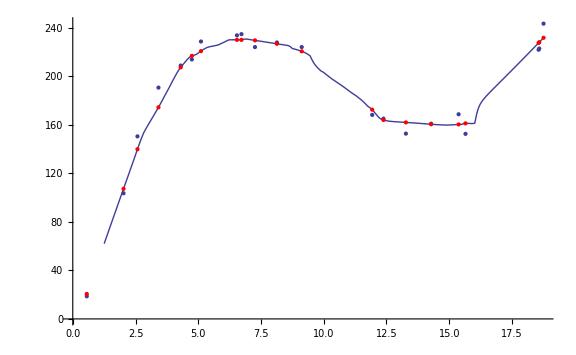

```mathematica
Show[scatterPlot,loessPlot,expectedPlot]
```

## Tricube Weighting Function

Below is a plot of the Tricube weighting function used to scale the weight given to regression subset of scatter plot points.

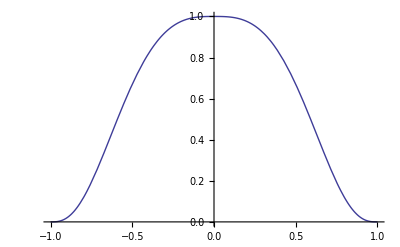

```mathematica
Plot[TricubeWeight[x],{x,-1,1}]
```